# Pyramidal Cyclope 1D (OverConstrainted)

Model where we reject solutions after one fail through scale iteration.
The undefined value will be cero.

```mathematica
SetOptions[InputNotebook[],AutoGeneratedPackage->Automatic]
```

```mathematica
SetDirectory[NotebookDirectory[]];
$Path=Append[$Path,FileNames["*",{ParentDirectory[]}]];
```

```mathematica
(* Package to obtain the pyramidal representation *)
<<"pyramid1d`"
```

## Test Points {line1, line2, pyrf12}

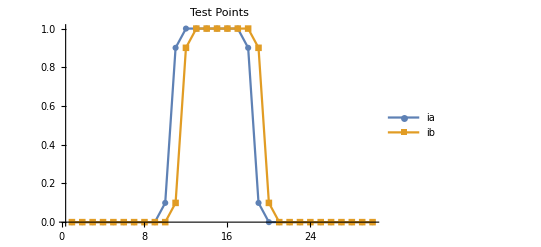

```mathematica
(* We create test points for compilation test *)
line1=GaussianFilter[Table[If[11<= p<=18,1,0],{p,1,30}],1];
line2=GaussianFilter[Table[If[11<= p<=18,1,0],{p,1-1,30-1}],1];
ListPlot[{line1, line2},Joined->True,PlotMarkers->Automatic,PlotRange->All,PlotLabel->"Test Points",PlotLegends->{"ia","ib"}]
```

```mathematica
(*generate functions of pyramid with pyrFuncGen*)
(* input-> {original points, number of levels}*)
(* Output-> {functions f and df for n+1 levels} *)
pyrf1=pyrFuncGen[line1,4];
pyrf2=pyrFuncGen[line2,4];
pyrf12=Flatten[{pyrf1, pyrf2}, {{2},{1},{3}}];

Plot[{pyrf12[[5,1,1]][x],pyrf12[[5,2,1]][x]},{x,1,30}];
```

## Pyramidal Flow 1D (PyrFlow1D)

### See Plot

```mathematica
(* Function to plot flow solution *)
(* Input-> {pixel of interest, range of plot from p, {initial value for v1, initial value for v2}, {functions a, da, b, db}}*)
(* Output-> Plot with graphics solutions *)

seePlot[p_,q_,{v1_,v2_},{{a_,da_},{b_,db_}}]:=Block[{c},(
c=(a[p]+b[p])/2;
Show[
Plot[{a[x],b[x]},{x,p-q,p+q}],
Graphics[{
Point[{{p,c},{p,a[p]},{p,b[p]}}],
Point[{{p-v1,c},{p+v2,c}}],
Line[{{p,a[p]},{p,b[p]}}],
Line[{{p-v1,c},{p+v2,c}}]
}]
]
)];

seePlot::usage="
Function to plot flow solution
Input→ {p, q, {v1, v2}, {{a,da},{b,db}}}
Output-> a and b plot with v1 and v2 solutions
p= Pixel of interest
q= Range to plot from pixel of interest
v1= Solution for a
v2= Solution for b
{a, da}= {function of a, derivative of function of a}
{b, db}= {function of b, derivative of function of b}
";
```

### PyrUpgrade1D

```mathematica
(* Function to update values of v1 and v2 with Over Constrained standards *)
(* Any value that does not meets the constraints becomes 0 *)

(* Input-> {{initial values for v1, v2 and status}, pixel of interest, {functions f1, df1, f2, df2}, threshold for magnitude error}*)
(* Output-> {new values for v1, v2 and status} *)
PyrUpgrade1D[{v1_,v2_,status_},p0_, {{fline1_,dfline1_} ,{fline2_,dfline2_}}, threshold_]:=Block[{p1, p2, c,d1,d2,dv1,dv2},(

p1=p0-v1;
p2=p0+v2;

c = (fline1[p0]+fline2[p0])/2;
d1=dfline1[p1];
d2=dfline2[p2];

(* d1 and d2 have to be the same sign in every iteration *)
If[d1*d2 <0, Return[{0,0,"sign"}]];

(* magnitude needs to be bigger than threshold every iteration *)
If[(Abs[d1]<threshold||Abs[d2]<threshold ),Return[{0,0,"mag"}]];

(* Change of sign during iteration *)
If[(dfline1[p0]*d1<0||dfline2[p0]*d2<0),Return[{0,0,"flip"}]];


(* dv1,dv2 : step from last {v1,v2} to new {v1,v2} *)
{dv1,dv2}= {(fline1[p1]-c)/d1,(c-fline2[p2])/d2};

(* status: "OK" -> solution respects constraints,  errors: "sign", "mag", "flip" *)
(* status: "converged" -> we converged!! *)
{v1+dv1,v2+dv2,If[Norm[{dv1,dv2}]<0.001,"converged","ok"]}
)];

(* No other solution will be calculated when status records an error message in this pyramidal level*)
PyrUpgrade1D[{v1_,v2_,"sign"},p0_, {{fline1_,dfline1_} ,{fline2_,dfline2_}}, threshold_]:={0,0,"sign"};
PyrUpgrade1D[{v1_,v2_,"mag"},p0_, {{fline1_,dfline1_} ,{fline2_,dfline2_}}, threshold_]:={0,0,"mag"};
PyrUpgrade1D[{v1_,v2_,"flip"},p0_, {{fline1_,dfline1_} ,{fline2_,dfline2_}}, threshold_]:={0,0,"flip"};

PyrUpgrade1D::usage="
Function to update values of v1 and v2 with OverConstrained standards
Input→ [{v1,v2,status},p0,{{f1,df1},{f2,df2},threshold}
Output-> {v1,v2,status}
v1= Solution of f1
v2= Solution of f2
status= Status of the solution (ok, sign, mag, flip, converged)
p0= point of interest
{f1,df1}={function 1, derivative of function 1}
{f2,df2}={function 2, derivative of function 2}
threshold= threshold to respect magnitude constraint
";
```

### Test

```mathematica
(* initial values *)
{v1, v2}={0.,0.};
status="ok";
i=0;
p=19;
```

```mathematica
(*Test for PyrUpgrade1D, manual test to iterate multiple times*)
(* n is the level of pyramid *)
n=1;
{v1,v2,status}=PyrUpgrade1D[{v1,v2,status},p, pyrf12[[n]],0.01]
```

{0.723034,0.722992,ok}

```mathematica
(* see *)
seeplot[p,2,{v1,v2},pyrf12[[n]]];
```

### PyrFlow1D

```mathematica
(* Function to find solutions for all levels of pyramid {l1,l2,l3,l4,...} or {l1} *)
(* Input-> {number of iterations, pixel of interests, pyrfunctions,threshold *)
(* Output-> {v1, v2,status}*)
PyrFlow1D[i_, p0_, pyrfunctions_,threshold_]:=Block[{v1, v2,c,status},(
c=Length[pyrfunctions]-1; (* number of levels *)

status="ok";
{v1, v2}={0.,0.};

Do[
(* compute at this scale, using current motion estimate *)
{v1,v2,status}=Nest[PyrUpgrade1D[#,p0, pyrfunctions[[-f]],threshold*2^(-c)]&,{v1,v2,status},i];

c=c-1

,{f,1,Length[pyrfunctions]}];

{v1, v2,status}
)];

PyrFlow1D::usage="
Function to update values of v1 and v2 over all levels of a pyramidal function representation
with OverConstrained standards.
Input→ [i, p0, pyrfunctions, threshold]
Output-> {v1, v2, status}
i= number of iterations
p0= point of interest
pyrfunctions= list with the dimensions of {pyrlvl, number of image(1 or 2), kind of function(f or df)}
where pyrlvl is the pyramidal level
threshold= threshold to respect magnitude constraint
v1= Solution of f1
v2= Solution of f2
status= Status of the solution (ok, sign, mag, flip, converged)
";
```

#### Test

0.01*2^(-m) depends on m to update the error depending on the highest resolution scale

```mathematica
(* Initializing values *)
{v1, v2}={0.,0.};
i=10;
p=19;

(* m-> max lvl, n-> min lvl *)
m=5;
n=5;

(*PyrFlow1D solution*)
{v1,v2,status}=PyrFlow1D[i, p,pyrf12[[m;;n]],0.0001*2^(-m+1)]
{Total[{v1,v2}],status}
```

{0.315902,0.37899,converged}

{0.694891,converged}

```mathematica
(* see *)
seeplot[p,2,{v1,v2},pyrf12[[m]]];
Plot[{pyrf12[[m,1,2]][x],pyrf12[[m,2,2]][x]},{x,p-2,p+2}];
```

## Graphics for one pixel iteration (pixelIterGraphics)

### One Pixel Iteration

```mathematica
(* Makes iterations and saves all the values *)
pixelIter[i_, p0_, pyrfunctions_,threshold_]:=Block[{v1, v2,c,status,iterTable},(

c=Length[pyrfunctions]-1; (* number of levels *)
status="ok";
{v1, v2}={0.,0.};

Table[
(* compute at this scale, using current motion estimate *)

iterTable=Table[
(*index of pyrfunction works only if fed the right range of pyrfunctions*)
{v1,v2,status}=PyrUpgrade1D[{v1,v2,status},p0, pyrfunctions[[-f]],threshold*2^(-c)]
,{j,1,i}];

c=c-1;
iterTable
,{f,1,Length[pyrfunctions]}]

)];

pixelIter::usage="
Makes iterations with OverConstrained standards and saves all the values
Input→ [i, p0, pyrfunctions, threshold]
Output-> list with the dimensions of: {lvls, i, {v1, v2, status}}
i= number of iterations
p0= point of interest
pyrfunctions= list with the dimensions of {pyrlvl, number of image(1 or 2), kind of function(f or df)}
where pyrlvl is the pyramidal level
threshold= threshold to respect magnitude constraint
v1= Solution of f1
v2= Solution of f2
status= Status of the solution (ok, sign, mag, flip, converged)
";
```

#### Test

```mathematica
iter=pixelIter[10, 11, pyrf12[[4 ;; 5]],0.001]
```

{{{0.896616,0.691742,ok},{0.765046,0.792656,ok},{0.762131,0.794845,ok},{0.76213,0.794846,converged},{0.76213,0.794846,converged},{0.76213,0.794846,converged},{0.76213,0.794846,converged},{0.76213,0.794846,converged},{0.76213,0.794846,converged},{0.76213,0.794846,converged}},{{0.438928,0.377466,ok},{0.432183,0.392558,ok},{0.432179,0.392576,converged},{0.432179,0.392576,converged},{0.432179,0.392576,converged},{0.432179,0.392576,converged},{0.432179,0.392576,converged},{0.432179,0.392576,converged},{0.432179,0.392576,converged},{0.432179,0.392576,converged}}}

### One level Pixel Iteration Graphics

```mathematica
(* Makes plots only for one level *)
(* input:{currentlvl, each iteration v, pixel of interest, pixel range for plots, functions of current lvl}*)
oneLevelPixelIterGraphics[lvl_,iter_, p0_,prange_, {{flineia_,dflineia_},{flineib_,dflineib_}}]:=Block[{c,iterTable},(

(* c values *)
c=(flineia[p0]+flineib[p0])/2;

iterTable=Table[
Labeled[
Show[
(* Plot Graphic *)
Plot[{flineia[x],flineib[x]},{x,p0-prange,p0+prange},PlotLegends->{"ia","ib"}],

Graphics[{
PointSize[0.01],
(* c line *)
Line[{{p0,flineia[p0]},{p0,flineib[p0]}}],
If[iter[[i,3]]=="sign",Red,
If[iter[[i,3]]=="mag",Purple,
If[iter[[i,3]]=="flip",Orange,Black]]
],
(* c point *)
Point[{p0,c}],
{Arrowheads->Small,Arrow[{{p0-iter[[i,1]],c},{p0+iter[[i,2]],c}}]}
}],
ImageSize->Scaled[0.5]
],
(* Label *)
Style[Framed[GraphicsColumn[{
Row[{"Current dv= ", Total[{iter[[i,1;;2]]}]}],
Row[{"Current iteration= ",i}],Row[{"Current level= ",lvl}]}]]]]
,{i,1,Length[iter]}]

)]

oneLevelPixelIterGraphics::usage="
Makes plots for the intermediate solutions of a pyramidal level
Input→ [lvl, iter, p0, prange, {{flineia, dflineia},{flineib, dflineib}}]
Output-> list with the dimensions of: {i, Plot of flineia and flineib with solution v1 and v2}
lvl= current pyramidal level
iter= solutions with the form {lvls, i, {v1, v2, status}
p0= pixel of interest
prange= range for plot from p0
{{flineia, dflineia},{flineib, dflineib}}= Current level functions 
";
```

#### Test

```mathematica
oneLevelPixelIterGraphics[5,iter[[1]], 11,3,  pyrf12[[5 ;; 5]][[1]]];
```

### All levels pixel iteration Graphics

```mathematica
(* Makes graphics for all levels*)
(* iterations, pixel of interest, plot range from pixel, max lvl,lvl's functions, threshold}*)
pixelIterGraphics[i_, p0_,prange_, maxlvl_,pyrfunctions_,threshold_]:=Block[{iter},(
(* Makes iterations by saving all the values *)
iter=pixelIter[i,p0, pyrfunctions,threshold];

Flatten[Table[
(* Makes plots only for one level *)
oneLevelPixelIterGraphics[maxlvl-j+1,iter[[j]], p0,prange,  pyrfunctions[[-j ;;-j]][[1]]]
,{j,1,Length[iter]}]]
)]

pixelIterGraphics::usage="
Makes plots for the intermediate solutions of a pyramidal level
Input→ [i, p0, prange, maxlvl, pyrfunctions threshold]
Output-> list with the dimensions of: {lvls*i, Plot of flineia and flineib with solution v1 and v2}
";
```

#### Test

```mathematica
ListAnimate[pixelIterGraphics[10, 11,3,5, pyrf12[[4;; 5]],0.001]]
```

## Graphics for All pixels

### All Pixel Graphics

```mathematica
lineTest[rangex_,pyrab_,threshold_]:=Block[{v1,v2,status},(
Table[
{v1,v2,status}=PyrFlow1D[10,x,pyrab,threshold]

,{x,rangex}]
)]

pixelIterGraphics::usage="
Input→ [rangex, pyrab, threshold]
Output-> {rangex, {v1,v2,status}}
";
```

#### Test

```mathematica
tes1=lineTest[Range[1,Length[line1]],pyrf12[[5;;5]],0.001]
```

{{0.412818,0.414549,converged},{0.421265,0.422398,converged},{0.431408,0.431875,converged},{0.443644,0.443372,converged},{0.458585,0.457505,converged},{0.477194,0.475272,converged},{0.501049,0.498372,converged},{0.532873,0.529918,converged},{0.577744,0.576303,converged},{0.646162,0.653233,converged},{0.76213,0.794846,converged},{0.966144,1.1436,converged},{0,0,mag},{0,0,sign},{0,0,mag},{-0.0141763,-0.0236911,converged},{0.142234,0.194386,converged},{0.242991,0.305343,converged},{0.315902,0.37899,converged},{0.373045,0.434424,converged},{0.420347,0.479254,converged},{0.461,0.517122,converged},{0.496846,0.549972,converged},{0.528997,0.578904,converged},{0.558141,0.604557,converged},{0.584702,0.62729,converged},{0.608927,0.647278,converged},{0.630934,0.664561,converged},{0.65074,0.679073,converged},{0.668273,0.690652,converged}}

### See All pixels in line

```mathematica
seeAllLine[rangex_, {lvlmin_,lvlmax_},pyrab_,threshold_]:=Block[{tRun,lineia,dlineia,lineib,dlineib,cTable,c,g0},(

tRun=lineTest[rangex,pyrab[[lvlmin;;lvlmax]],threshold];

{lineia,dlineia}=pyrab[[lvlmin,1]];
{lineib,dlineib}=pyrab[[lvlmin,2]];

i=1;
cTable=Table[
c=(lineia[p]+lineib[p])/2;
g0=Graphics[{
PointSize[0.01],
Line[{{p,lineia[p]},{p,lineib[p]}}],
If[tRun[[i,3]]=="sign",Red,
If[tRun[[i,3]]=="mag",Purple,
If[tRun[[i,3]]=="flip",Orange,Black]]
],
Point[{p,c}],
{Arrowheads->Small,Arrow[{{p-tRun[[i,1]],c},{p+tRun[[i,2]],c}}]}
}];
i=i+1;
g0
,{p,rangex}];

Show[
Plot[{lineia[x],lineib[x]},{x,rangex[[1]],rangex[[-1]]},PlotLegends->{"ia","ib"}],
cTable,
(*,
PlotLabel->info,*)
ImageSize->Scaled[0.5]
]
)]

seeAllLine::usage="
Input→ [rangex, {lvlmin,lvlmax}, pyrab, threshold]
Output-> Plot with solutions in rangex
";
```

#### Test

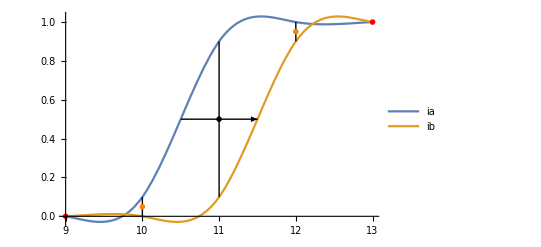

```mathematica
seeAllLine[Range[9,13],{1,5},pyrf12,0.001]
```